# The Energy Function of ^163 Lu

## Computing the Energy Function ℋ(I,θ,φ) for the nucleus

## ℋ=I/2(A_1+A_2)+A_3 I^2+I(I-1/2)sin^2 θ(A_1 cos^2 φ+A_2 sin^2 φ-A_3)+j/2(A_2+A_3)+A_1 j^2-2 A_1 Ij sin^2 θ-V(2j-1)/(j+1)sin(γ+π/6);

### Constants

```mathematica
A1=0.1;
A2=0.4;
A3=0.2;
V=8.5;
j=13/2;
γ=20;
```

### Expression

```mathematica
Hen[I_,θ_,φ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ*π/180]^2(A1*Cos[φ*π/180]^2+A2*Sin[φ*π/180]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ*π/180]-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
```

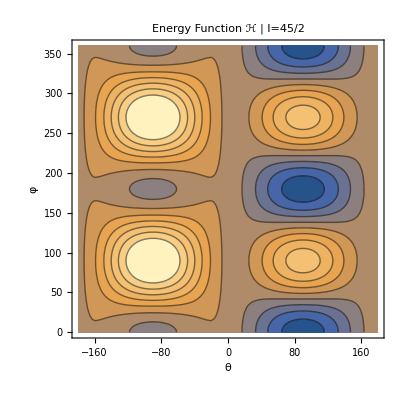

```mathematica
p1=ContourPlot[Hen[22.5,θ,φ],{θ,-180,180},{φ,0,360},Frame->True,FrameStyle->Directive[Black,Thick],Contours->10,FrameLabel->{"θ","φ"},PlotLabel->"Energy Function ℋ | I=45/2",LabelStyle->{15,Black,Bold,FontFamily->"Times New Roman"}];
Show[p1]
(*Save the graph with the Contour Plot to an output file*)
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/ContourPlot.jpeg",p1];
```